```mathematica
ϕcut:=10^(-3); 
UVcutQs:=1; (*Momentum is measured in units of gμ *)
S1[x_?NumberQ,y_?NumberQ]:=4NIntegrate[t BesselK[0,2 t] BesselI[0,2x^2 1/((x^2+y^2) (2+x^2+y^2)) t]^2BesselI[0,2y^2 1/((x^2+y^2)(2+x^2+y^2))t]^2,{t,0,Infinity}]; 

 DensitySiMinusSr[x_?NumberQ,y_?NumberQ]:=((1+2/(x^2+y^2))^2)/(1+4/(x^2+y^2))1/S1[x,y];
SiMinusSr[UVcut_?NumberQ]:=1/(4 π^2)4 NIntegrate[q Log[DensitySiMinusSr[q Cos[ϕ],q Sin[ϕ]]],{q,10^(-4),UVcut},{ϕ,ϕcut,π/2-ϕcut}]
Sr[UVcut_?NumberQ]:=1/(2 π)NIntegrate[q Log[1+4/q^2],{q,10^(-4),UVcut}]
```

```mathematica
SiMinusSr[UVcutQs]/Sr[UVcutQs] (*Ratio *)
```

0.361861

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

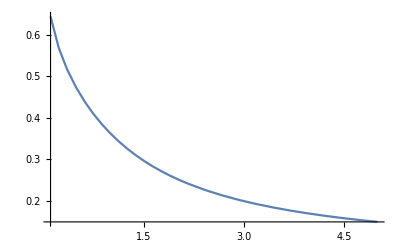

```mathematica
Plot[SiMinusSr[x]/Sr[x],{x,0.1,5},MaxRecursion->1,PlotPoints->20]
```